## This is all just set up for plotting the vert_hom_inlattice_long

```mathematica
SetDirectory[NotebookDirectory[]]
ClearAll[RawDatas,FitParams,ExpVar]
Needs["ErrorBarPlots`"]
```

Z:\Data\2015\03Mar15\23\MLFit

```mathematica
(*
Averaged over sites X=126-127,Y=130-131;
From Data = Z:\Data\2015\03Mar15\23\MLFit;
*)
RawDatas=Import["RawData.csv"]
FitParams=Import["FitParamsWError.csv"]
ExpVar=Import["ExpVar.csv"]
Datas=Import["Data.csv"]
```

{{1,-0.090639,0.090639},{0.5098,0,0},{0.17778,-0.051525,0.060699},{0.044444,-0.024404,0.039724},{0.15385,-0.04563,0.054571},{0.425,-0.074299,0.078006},{0.79167,-0.062208,0.054025},{0.97674,-0.03486,0.01524},{0.83721,-0.061658,0.050566},{0.61905,-0.075961,0.072335},{0.32558,-0.067064,0.073216},{0.068182,-0.03211,0.044043},{0.020408,-0.014396,0.029692},{0.34884,-0.068276,0.074008},{0.5814,-0.076385,0.073915},{0.94737,-0.045565,0.028583},{1,-0.028056,0},{0.79592,-0.060447,0.053781},{0.53333,-0.074415,0.071877},{0.19048,-0.054204,0.066037},{0.05,-0.027956,0.042184},{0.25,-0.063627,0.070641}}

{{1.0306,-0.020612,0.020612},{0.947,-0.02841,0.01894},{4.935,-0.04935,0.074025},{1.648,-0.090639,0.090639}}

{{0,0.01,0.15,0.3,0.45,0.6,0.75,0.9,1.05,1.2,1.35,1.5,1.65,1.8,1.95,2.1,2.25,2.4,2.55,2.7,2.85,3}}

{{0,1,-0.090639,0.090639},{0.01,0.5098,0,0},{0.15,0.17778,-0.051525,0.060699},{0.3,0.044444,-0.024404,0.039724},{0.45,0.15385,-0.04563,0.054571},{0.6,0.425,-0.074299,0.078006},{0.75,0.79167,-0.062208,0.054025},{0.9,0.97674,-0.03486,0.01524},{1.05,0.83721,-0.061658,0.050566},{1.2,0.61905,-0.075961,0.072335},{1.35,0.32558,-0.067064,0.073216},{1.5,0.068182,-0.03211,0.044043},{1.65,0.020408,-0.014396,0.029692},{1.8,0.34884,-0.068276,0.074008},{1.95,0.5814,-0.076385,0.073915},{2.1,0.94737,-0.045565,0.028583},{2.25,1,-0.028056,0},{2.4,0.79592,-0.060447,0.053781},{2.55,0.53333,-0.074415,0.071877},{2.7,0.19048,-0.054204,0.066037},{2.85,0.05,-0.027956,0.042184},{3,0.25,-0.063627,0.070641}}

```mathematica
FitFunc[A_,B_,F_,ϕ_,t_]:=FitFunc[A,B,F,ϕ,t]=1/2(A+B Cos[F t + ϕ ])
```

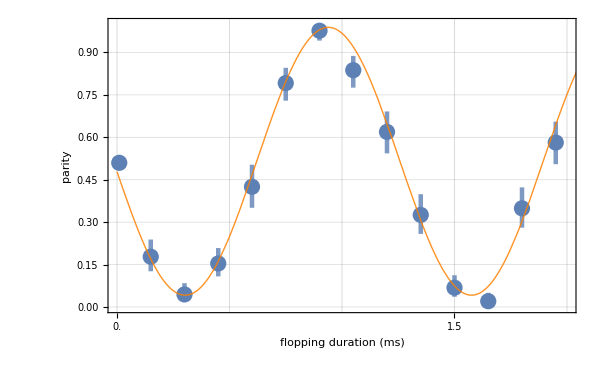

vert_HOM.png

```mathematica
prefix="vert_HOM";
Datay=RawDatas[[;;,1]];
Errors=RawDatas[[;;,2;;3]];
Dataxy=Datas[[;;,1;;2]];
Needs["ErrorBarPlots`"]
floppoints=Table[{{Dataxy[[ii,1]],Dataxy[[ii,2]]},ErrorBar[{Errors[[ii,1]],Errors[[ii,2]]}]},{ii,2,15}];
SetOptions[ListPlot,
Joined->True,
Frame->True,
PlotRange->{{0,2},{0,1}},
FrameTicks->{{Automatic,None},{Table[{ii 0.5, ii 0.5},{ii,0,20,1}],None}},GridLines->{Table[ii 0.5,{ii,0,20,1}],Automatic}];
Show[ErrorListPlot[floppoints,Joined->False,
FrameLabel->{"flopping duration (ms)","parity","t_offset =   ms,   f_Rabi =  Hz","Contrast = 95±_2^3%"},
ImageSize->600,
FrameStyle->Directive[FontSize->20],ErrorBarFunction->Function[{coords,errs},{Opacity[0.8],Rectangle[coords+{-0.01,errs⟦2,1⟧},coords+{0.01,errs⟦2,2⟧}]}]],Plot[FitFunc[FitParams⟦1,1⟧,FitParams⟦2,1⟧,FitParams⟦3,1⟧,FitParams⟦4,1⟧,x],{x,0,ExpVar⟦1,Length[ExpVar⟦1,;;⟧]⟧},PlotStyle-> {Thick,Orange,Opacity[0.85]}]]
Export[prefix<>".png",%]
```

```mathematica
4.935/(2*π)
```

0.78543

```mathematica
-0.04935/(2*π)
0.074025/(2*π)
```

-0.0078543

0.0117814

```mathematica
-0.068252/(2*π)
0.091003/(2 π)

1.648/4.935
-0.090639/4.935
```

-0.0108626

0.0144836

0.333941

-0.0183666

```mathematica
N[1.0451/5.6877]
```

0.183747

```mathematica
N[-0.11197/5.6877]
N[0.091236/5.6877]
```

-0.0196863

0.0160409

```mathematica
2.4399/(2*π)
```

0.388322

```mathematica
0.024399/(2*π)
```

0.00388322

```mathematica
N[3.8726-π]/2.4399
N[0.077452/2.4399]
```

0.299605

0.0317439